2181.66

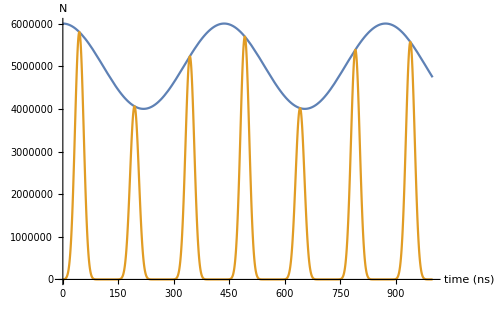

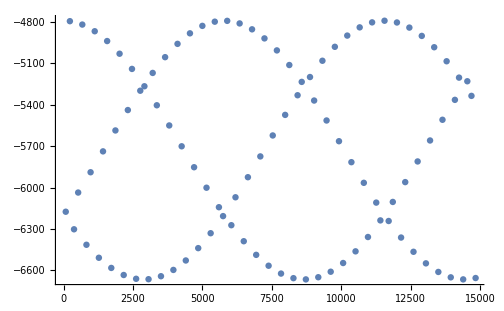

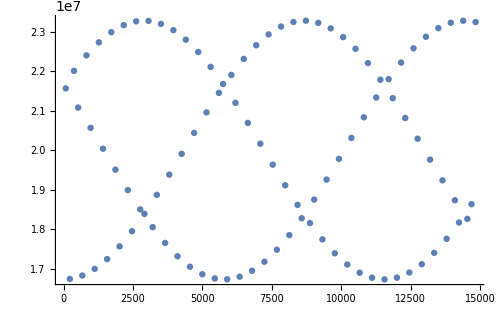

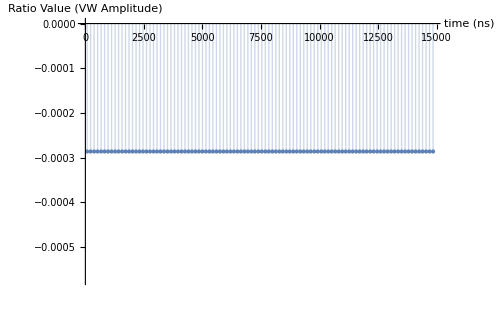

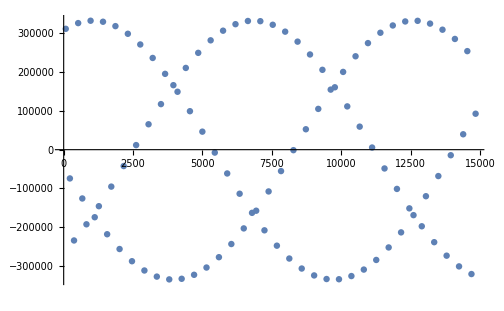

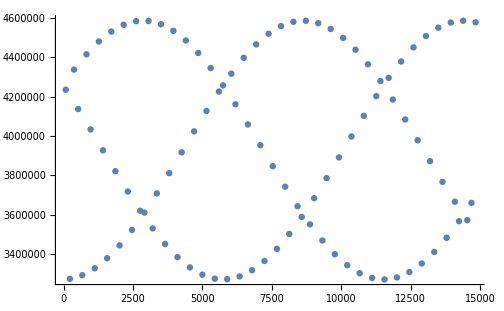

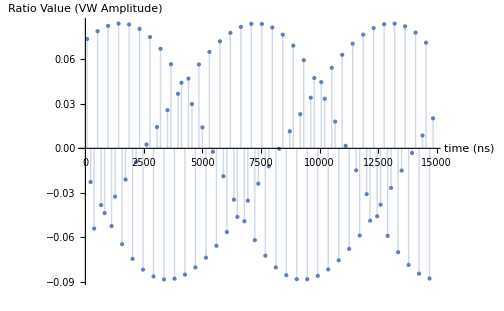

1.09651×10^14

```mathematica
Clear[ωa,binWidth,N0,τ,Avw,τVW,ωVW,ϕVW,ωFR,ϕFR,timeShift];
ωa=0.00144;
binWidth=149.2;
N0 =5*10^6;
τ=64440;
Avw=0.2;
τVW=250000000;
(*ωVW=10.06*ωa;*)
ωVW=10.0*ωa;
ϕVW=0;
ωFR=Pi/binWidth;
ϕFR=Pi/5;
timeShift=Pi/ωa
(*timeShift=Pi/ωa + (20* binWidth / 5)*)
nBins = 100;
maxTime = binWidth *nBins;
binShift=0;

f[t_]:=N0*Exp[-t/τVW]*(1+Avw*Cos[ωVW*t+ϕVW]);
fFR[t_]:=f[t]*Sin[ωFR*t+ϕFR]^16;

Plot[{f[x],fFR[x]},{x,0,1000}, AxesLabel->{"time (ns)", "N"}]

Clear[data,dataFR]
data=Table[{binWidth*( i + 1/2),NIntegrate[f[x],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth},{i,0,nBins-1}];
dataFR=Table[{binWidth*( i + 1/2),NIntegrate[fFR[x],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth},{i,0,nBins-1}];
(*datatemppp=Table[{binWidth*( i + 1/2),f[binWidth*( i + 1/2)]},{i,0,nBins-1}];*)
ListPlot[{data,dataFR},Filling->Axis,PlotRange->{0,1*10^7}];

diffData = data;
diffData[[All,2]]=diffData[[All,2]]/dataFR[[All,2]];
ListPlot[diffData];

U=Table[{binWidth*( i + 1/2),Exp[timeShift/τ]*NIntegrate[f[x+timeShift],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth + Exp[-timeShift/τ]*NIntegrate[f[x-timeShift],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth },{i,0,nBins-1}];
V=Table[{binWidth*( i + 1/2),NIntegrate[f[x],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth + NIntegrate[f[x],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth },{i,0,nBins-1}];
ListPlot[{U,V}];

num = data;
num[[All,2]]=(V[[All,2]]-U[[All,2]]);
ListPlot[num]
denom = data;
denom[[All,2]]=(V[[All,2]]+U[[All,2]]);
ListPlot[denom]

R = data;
R[[All,2]]=(V[[All,2]]-U[[All,2]])/(V[[All,2]]+U[[All,2]]);
ListPlot[R,PlotStyle->PointSize[Large], Filling->Axis, AxesLabel->{"time (ns)", "Ratio Value (VW Amplitude)"}]


UFR=Table[{binWidth*( i + 1/2),Exp[timeShift/τ]*NIntegrate[fFR[x+timeShift],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth + Exp[-timeShift/τ]*NIntegrate[fFR[x-timeShift],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth },{i,0,nBins-1}];
VFR=Table[{binWidth*( i + 1/2),NIntegrate[fFR[x],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth + NIntegrate[fFR[x],{x,i*binWidth+binShift,(i+1)*binWidth+binShift}]/binWidth },{i,0,nBins-1}];
ListPlot[{UFR,VFR}];

numFR = data;
numFR[[All,2]]=(VFR[[All,2]]-UFR[[All,2]]);
ListPlot[numFR]
denomFR = data;
denomFR[[All,2]]=(VFR[[All,2]]+UFR[[All,2]]);
ListPlot[denomFR]

RFR = data;
RFR[[All,2]]=(VFR[[All,2]]-UFR[[All,2]])/(VFR[[All,2]]+UFR[[All,2]]);
ListPlot[RFR,PlotStyle->PointSize[Large], Filling->Axis, AxesLabel->{"time (ns)", "Ratio Value (VW Amplitude)"}]

diffR= RFR;
diffR[[All,2]]=diffR[[All,2]]/R[[All,2]];
ListPlot[diffR];
(Max[RFR[[All,2]]]-Min[RFR[[All,2]]])/(Max[R[[All,2]]]-Min[R[[All,2]]])
```

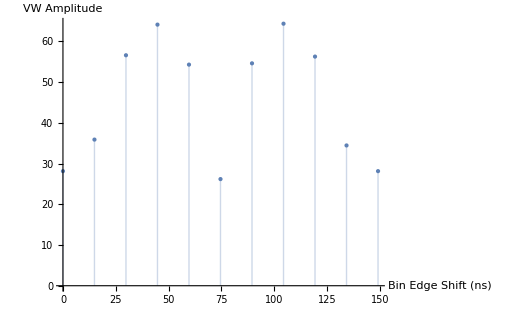

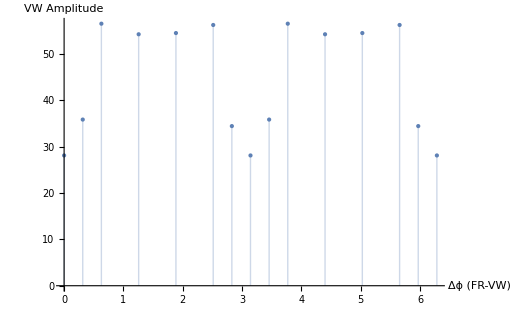

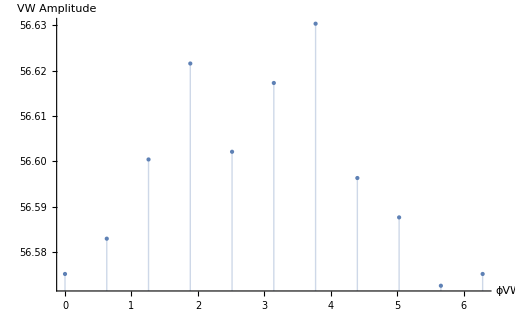

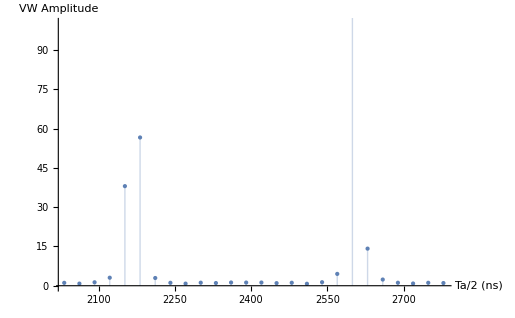

```mathematica
(*Scan over bin edge shift, with ωVW=10.06*ωa, ϕVW=0.5, ϕFR=0, binWidth=149.2, in steps of binWidth/10*)
binShiftScan={{0,28.137},{14.92,35.8865},{29.84,56.5963},{44.76,64.1205},{59.68,54.2979},{74.6,26.1884},{89.52,54.6127},{104.44,64.35},{119.36,56.2718},{134.28,34.4493},{149.2,28.137}};
ListPlot[binShiftScan,PlotStyle->PointSize[Large], Filling->Axis, AxesLabel->{"Bin Edge Shift (ns)", "VW Amplitude"}]

(*Scan over relative phases with ωVW=10.06*ωa, ϕVW=0, ϕFR changing, binWidth=149.2, binShift=0, in steps of 2Pi/10, with some extra points added*)
relPhaseScan = {{0,28.1262},{Pi/5,56.5751},{2Pi/5,54.289},{3Pi/5,54.5533},{4Pi/5,56.2957},{Pi,28.1262},{6Pi/5,56.5751},{7Pi/5,54.289},{8Pi/5,54.5533},{9Pi/5,56.2957},{2Pi,28.1262},{5.5Pi/5,35.8757},{4.5Pi/5,34.4639},{9.5Pi/5,34.4639},{0.5Pi/5,35.8757}};
ListPlot[relPhaseScan,PlotStyle->PointSize[Large], Filling->Axis, AxesLabel->{"Δϕ (FR-VW)", "VW Amplitude"}]

(*Putting the max points for the above two scans doesn't make it blow up, the max ratio difference is always around 64.*)

(*Scan over VW phases with ωVW=10.06*ωa, ϕFR=Pi/5, binWidth=149.2, binShift=0, in steps of 2Pi/10, with some extra points added*)
VWphaseScan={{0,56.5751},{Pi/5,56.5829},{2Pi/5,56.6004},{3Pi/5,56.6216},{4Pi/5,56.6021},{Pi,56.6173},{6Pi/5,56.6304},{7Pi/5,56.5963},{8Pi/5,56.5876},{9Pi/5,56.5725},{2Pi,56.5751}};
ListPlot[VWphaseScan,PlotStyle->PointSize[Large], Filling->Axis, AxesLabel->{"ϕVW", "VW Amplitude"}]

(*9x frequency ratio difference is always very close to 1.*)

(*Scan over timeShift around timeShift=Pi/ωa with ωVW=10.06*ωa, ϕVW=0, ϕFR=Pi/5, binWidth=149.2, binShift=0, in steps of binWidth/5, from -5/5 to 20/5*)
timeShiftScan={{2032.46,1.10379},{2062.3,0.812449},{2092.14,1.31021},{2121.98,3.0625},{2151.82,38.0031},{2181.66,56.5751},{2211.5,2.94899},{2241.34,1.11855},{2271.18,0.80905},{2301.02,1.15801},{2330.86,1.02753},{2360.7,1.22756},{2390.4,1.20917},{2420.38,1.21826},{2450.22,0.989005},{2480.06,1.13587},{2509.9,0.749577},{2539.74,1.33862},{2569.58,4.51542},{2599.42,601.737},{2629.26,14.163},{2659.1,2.36168},{2688.94,1.13578},{2718.78,0.848306},{2748.62,1.12264},{2778.46,1.02166}};
timeShiftScanPlot = ListPlot[timeShiftScan,PlotStyle->PointSize[Large], Filling->Axis, AxesLabel->{"Ta/2 (ns)", "VW Amplitude"}, PlotRange->All];
Show[timeShiftScanPlot, PlotRange->{0,100}]
```